## Constant Worker Population

Assumptions

The worker population is fixed sized.
Bad workers are replaced with novices.
Veterans remain in the worker population.
Worker/Buyer ratio fixed (gamma > 1)
The output is scaled to 1 (y factors out of V(t), so shouldn’t be a problem)

Discussion

It became clear that two types of constraints are necessary in this formulation of the problem. In addition to limiting the policy to the available veterans, you also have to limit to the available novices. Below are graphs of the worker/buyer system operating under different policies. Interesting behaviors arise as the veterans establish themselves in the population.

Looking at a few simple cases (theta=0.7, gamma=5, delta=0.9) for short times (t=3,4,5) it appears that the optimal policy is

```mathematica
Table[(1-theta)^i,{i,t}]
```

This policy appears to work for theta=0.2 and gamma down to 1. Random search was used to identify the optimal policies.

A derivation appears at the end of the notebook. The derivation hinges on the observation that increasing theta past the veterans limit, only decreases the production return for that time step. It also reduces the generation of veterans as well.

```mathematica
Needs["PlotLegends`"]
```

```mathematica
(* Compute state changes for a time step. 
Note, this function is used in a FoldList, hence the unused prod and last args. *)
ClearAll[UpdateVP]
UpdateVP[{prod_,vets_,last_}, (* state *)
x_, (* policy *)
theta_ (* goodness probability *),
gamma_ (* worker/buyer ratio*)]:= 
Block[{novices, p,jobs},
novices = 1-vets;
p =If[vets gamma< 1-x, (*veterans limit*)
1-vets  gamma,
If[(1-vets) gamma <x,(*novice limit*)
(1-vets) gamma,
x]];
{(1-p) + theta p, (* production *)
vets + theta p /gamma, (* veterans *)
 p (* acutal policy used *)}
]
```

Here are some examples of UpdateVP to make sure it passes the sniff test. Assume 100 workers 20 buyers with a goodness probability of 0.7.
First,  we look at the case with no known veterans. Of the lucky 20, 14 are good. So we should expect 14% veterans and production of 0.7.
Next, we consider the case where 10% of the workers are veterans. Buyers want 60% veterans, but should be limited to 50%.
Finally, 95% veterans, but buyers want 30% novice, and should only get 25% (5/20)

```mathematica
UpdateVP[{0,0,0},1,0.7,5]
UpdateVP[{0,0.1,0},0.6,0.7,5]
UpdateVP[{0,0.95,0},0.3,0.7,5]
```

{0.7,0.14,1}

{0.82,0.184,0.6}

{0.925,0.985,0.25}

```mathematica
ClearAll[EvalPolicy]
(*Takes a policy and simulates the worker/buyer system*)
EvalPolicy[x_,theta_,gamma_] := Block[{},
FoldList[UpdateVP[#1,#2,theta,gamma]&, {0,0,0}, x]
]

ClearAll[ScorePolicy]
(*Computes the social surplus at the end of the policy. 
It's V(t) from the problem description.*)
ScorePolicy[res_List, delta_]:=Block[{},
Fold[{#1[[2]] #2[[1]]+#1[[1]],#1[[2]] delta}&,{0,1},res][[1]]
]

ClearAll[GraphPolicy]
GraphPolicy[policy_,theta_,gamma_,delta_]:=Block[{res},
res=EvalPolicy[policy,theta,gamma];
res = Drop[res,1];
Print["Score = ",ScorePolicy[res,delta]];
ListPlot[Append[Transpose[res],policy],{PlotRange->{0,1},
PlotMarkers->Automatic,PlotLegend->{"Production","Veterans","Actual Policy","Attempted Policy"},
LegendPosition->{-0.3,-1.1},
LegendSize->{1,0.5}}]
]
```

Score = 0.406977

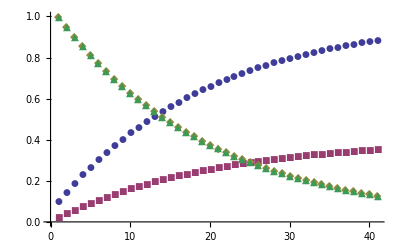

```mathematica
GraphPolicy[Table[0.95^i, {i,0,40}],0.1,5,0.6]
```

Score = 0.3175

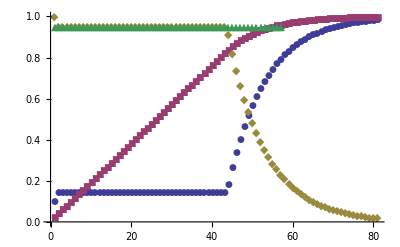

```mathematica
GraphPolicy[Table[0.95, {i,0,80}],0.1,5,0.6]
```

Score = 0.538152

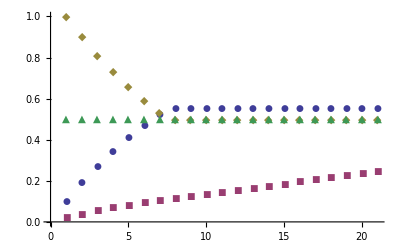

```mathematica
GraphPolicy[Table[0.5, {i,0,20}],0.1,5,0.6]
```

Score = 0.538182

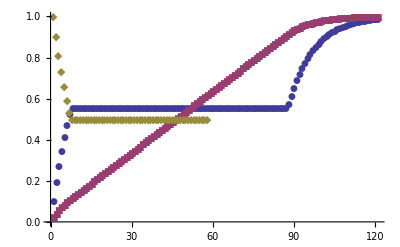

```mathematica
GraphPolicy[Table[0.5, {i,0,120}],0.1,5,0.6]
```

```mathematica
ClearAll[SearchScore]
SearchScore[policy_,theta_,gamma_,delta_]:=Block[{res,s},
res=EvalPolicy[policy,theta,gamma];
res = Drop[res,1];
s=ScorePolicy[res,delta];
{s,Last/@res}
]

ClearAll[Bound]
Bound[x_]:=Min[1,Max[0,x]]

ClearAll[Search]
Search[n_,iters_,theta_,gamma_,delta_]:=Block[{policy,best},
best=SearchScore[Table[Random[],{n}],theta,gamma,delta];
Print["Start =",best];
Do[
mutant=Bound/@(best[[2]]0+Table[Random[],{n}]);
(*Print[mutant];*)
cur=SearchScore[mutant,theta,gamma,delta];
(*Print[cur];*)
If[best[[1]]<cur[[1]],
Print["Best = ",cur];
best=cur],
{iters}];
Print[GraphPolicy[best[[2]],theta,gamma,delta]];
best
]
```

Start ={2.14663,{1,0.937751,0.0418892}}

Best = {2.28597,{1,0.379364,0.0889122}}

Best = {2.30713,{1,0.3,0.09}}

Score = 2.30713

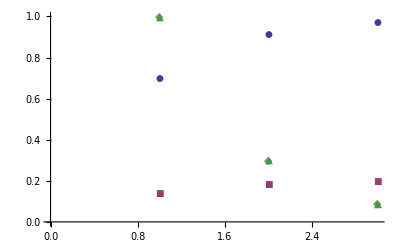

{2.30713,{1,0.3,0.09}}

```mathematica
bs3=Search[3,3000,0.7,5,0.9]
```

Start ={2.94477,{1,0.3,0.399959,0.0733619}}

Best = {2.97735,{1,0.32614,0.273278,0.0328368}}

Best = {2.97849,{1,0.364832,0.076305,0.198729}}

Best = {2.99674,{1,0.3,0.198685,0.0593576}}

Best = {3.01315,{1,0.3,0.09,0.105059}}

Best = {3.02142,{1,0.3,0.112656,0.0420813}}

Best = {3.0278,{1,0.344843,0.0586098,0.0175829}}

Best = {3.02869,{1,0.3,0.09,0.0340328}}

Best = {3.03023,{1,0.3,0.09,0.027}}

Score = 3.03023

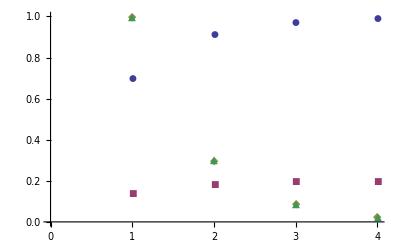

{3.03023,{1,0.3,0.09,0.027}}

```mathematica
bs4=Search[4,3000,0.7,5,0.9]
```

Start ={3.33909,{1,0.3,0.0966674,0.724236,0.981195}}

Best = {3.38247,{1,0.330326,0.134441,0.513502,0.906701}}

Best = {3.48873,{1,0.3,0.549026,0.316601,0.115417}}

Best = {3.62104,{1,0.3,0.22215,0.169584,0.0101326}}

Best = {3.62244,{1,0.3,0.09,0.0677952,0.279263}}

Best = {3.64786,{1,0.3,0.115695,0.166448,0.00873459}}

Best = {3.66325,{1,0.3,0.09,0.027,0.117225}}

Best = {3.66613,{1,0.314372,0.160147,0.0105093,0.014633}}

Best = {3.67367,{1,0.3,0.105981,0.0158133,0.0569778}}

Best = {3.68473,{1,0.3,0.09,0.027,0.0081}}

Score = 3.68473

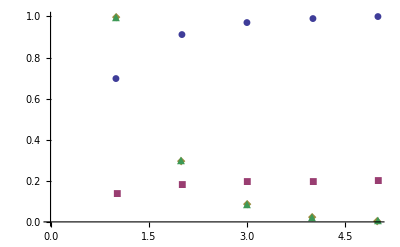

{3.68473,{1,0.3,0.09,0.027,0.0081}}

```mathematica
bs5=Search[5,5000,0.7,5,0.9]
```

Start ={1.48626,{1,0.953985,0.899331,0.429337,0.550255}}

Best = {1.63045,{1,0.8,0.695667,0.784066,0.344054}}

Best = {1.6564,{1,0.8,0.64,0.512,0.665633}}

Best = {1.79079,{1,0.8,0.64,0.512,0.4096}}

Score = 1.79079

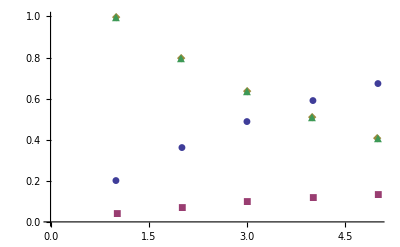

{1.79079,{1,0.8,0.64,0.512,0.4096}}

```mathematica
bs5=Search[5,5000,0.2,5,0.9]
```

Start ={1.79079,{1,0.8,0.64,0.512,0.4096}}

Score = 1.79079

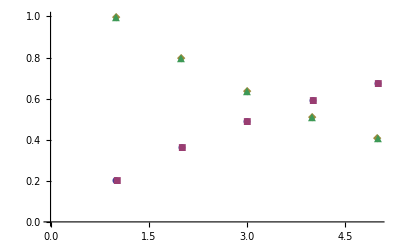

{1.79079,{1,0.8,0.64,0.512,0.4096}}

```mathematica
bs5=Search[5,5000,0.2,1,0.9]
```

Here’s a boundary-less progression to demonstrate how the state evolves.

```mathematica
UVP[{prod_,vets_,last_}, (* state *)
x_, (* policy *)
theta_ (* goodness probability *),
gamma_ (* worker/buyer ratio*)]:= 
Block[{},
{(1-x) + theta x, (* production *)
vets + theta x /gamma, (* veterans *)
 x (* acutal policy used *)}
]
```

```mathematica
ClearAll[theta,gamma]
UVP[{0,0,0},1,theta,gamma]
UVP[%,x[1],theta,gamma]
UVP[%,x[2],theta,gamma]
UVP[%,x[3],theta,gamma]
ScorePolicy[{%%%%,%%%,%%,%},delta]
```

{theta,theta/gamma,1}

{1-x[1]+theta x[1],theta/gamma+(theta x[1])/gamma,x[1]}

{1-x[2]+theta x[2],theta/gamma+(theta x[1])/gamma+(theta x[2])/gamma,x[2]}

{1-x[3]+theta x[3],theta/gamma+(theta x[1])/gamma+(theta x[2])/gamma+(theta x[3])/gamma,x[3]}

theta+delta (1-x[1]+theta x[1])+delta^2 (1-x[2]+theta x[2])+delta^3 (1-x[3]+theta x[3])

Derivation of optimal policy

Here’s the production (y) vs attempted policy (x). Notice how production drops once the veterans limit is met.

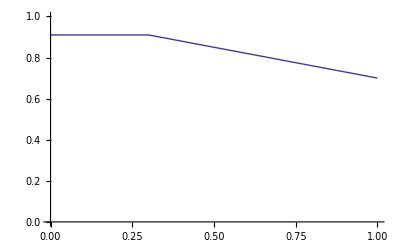

```mathematica
Plot[UpdateVP[{0,.14,0},x,.7,5][[1]],{x,0,1},{PlotRange->{0,1}}]
```

The veterans limit is at

```mathematica
vets gamma== 1-x
Solve[%]
```

gamma vets==1-x

{{x→1-gamma vets}}

The next veterans calculation is

```mathematica
vets + theta x /gamma
```

Or

```mathematica
Simplify[vets + theta (1-gamma vets)/gamma]
```

theta/gamma+vets-theta vets

Expressed as a recurrence, the veterans calculation is

```mathematica
vetsR[0]:=theta/gamma
vetsR[t_] :=theta/gamma +(1-theta)vetsR[t-1]
```

Whose closed form is

```mathematica
vetsC[t_]:=(theta/gamma )Sum[(1-theta)^i,{i,t}]+(theta/gamma)
```

Plugging this into the boundary constraint, we get

```mathematica
Simplify[1-gamma vetsC[t-1]]
```

(1-theta)^t